```mathematica
envelopeData[VisRnd005]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.05.env"];
envelopeData[VisRnd010]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.1.env"];
envelopeData[VisRnd015]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.15.env"];
envelopeData[VisRnd020]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.2.env"];
envelopeData[VisRnd025]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.25.env"];
envelopeData[VisRnd030]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.3.env"];
envelopeData[VisRnd035]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.35.env"];
envelopeData[VisRnd040]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.4.env"];
envelopeData[VisRnd045]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.45.env"];
envelopeData[VisRnd050]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.5.env"];
envelopeData[VisRnd055]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.55.env"];
envelopeData[VisRnd060]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.6.env"];
envelopeData[VisRnd065]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.65.env"];
envelopeData[VisRnd070]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.7.env"];
envelopeData[VisRnd075]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.75.env"];
envelopeData[VisRnd080]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.8.env"];
envelopeData[VisRnd085]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.85.env"];
envelopeData[VisRnd090]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.9.env"];
envelopeData[VisRnd095]=ReadDoubleData["/homes/tjakobi/PhD_Work/radialprojection/datafiles/random/visrnd-0.95.env"];
envelopeFct[VisRnd005]=Interpolation[normalizeEnvData[VisRnd005]];
envelopeFct[VisRnd010]=Interpolation[normalizeEnvData[VisRnd010]];
envelopeFct[VisRnd015]=Interpolation[normalizeEnvData[VisRnd015]];
envelopeFct[VisRnd020]=Interpolation[normalizeEnvData[VisRnd020]];
envelopeFct[VisRnd025]=Interpolation[normalizeEnvData[VisRnd025]];
envelopeFct[VisRnd030]=Interpolation[normalizeEnvData[VisRnd030]];
envelopeFct[VisRnd035]=Interpolation[normalizeEnvData[VisRnd035]];
envelopeFct[VisRnd040]=Interpolation[normalizeEnvData[VisRnd040]];
envelopeFct[VisRnd045]=Interpolation[normalizeEnvData[VisRnd045]];
envelopeFct[VisRnd050]=Interpolation[normalizeEnvData[VisRnd050]];
envelopeFct[VisRnd055]=Interpolation[normalizeEnvData[VisRnd055]];
envelopeFct[VisRnd060]=Interpolation[normalizeEnvData[VisRnd060]];
envelopeFct[VisRnd065]=Interpolation[normalizeEnvData[VisRnd065]];
envelopeFct[VisRnd070]=Interpolation[normalizeEnvData[VisRnd070]];
envelopeFct[VisRnd075]=Interpolation[normalizeEnvData[VisRnd075]];
envelopeFct[VisRnd080]=Interpolation[normalizeEnvData[VisRnd080]];
envelopeFct[VisRnd085]=Interpolation[normalizeEnvData[VisRnd085]];
envelopeFct[VisRnd090]=Interpolation[normalizeEnvData[VisRnd090]];
envelopeFct[VisRnd095]=Interpolation[normalizeEnvData[VisRnd095]];
```

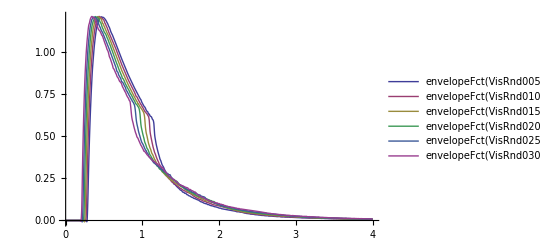

```mathematica
Plot[{envelopeFct[VisRnd005][t],envelopeFct[VisRnd010][t],
envelopeFct[VisRnd015][t],envelopeFct[VisRnd020][t],
envelopeFct[VisRnd025][t],envelopeFct[VisRnd030][t]},{t,0,4},PlotLegends->"Expressions"]
```

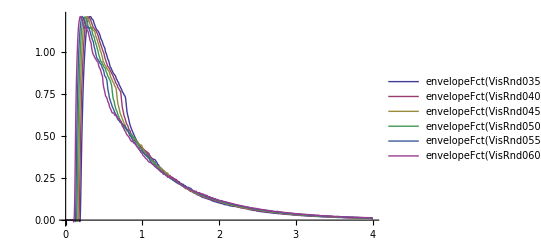

```mathematica
Plot[{envelopeFct[VisRnd035][t],envelopeFct[VisRnd040][t],
envelopeFct[VisRnd045][t],envelopeFct[VisRnd050][t],
envelopeFct[VisRnd055][t],envelopeFct[VisRnd060][t]},{t,0,4},PlotLegends->"Expressions"]
```

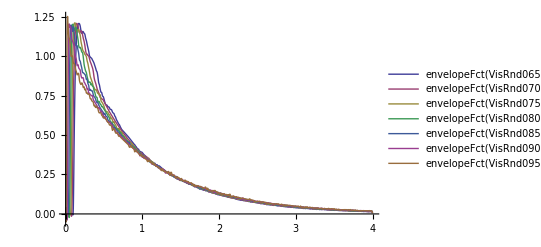

```mathematica
Plot[{envelopeFct[VisRnd065][t],envelopeFct[VisRnd070][t],
envelopeFct[VisRnd075][t],envelopeFct[VisRnd080][t],
envelopeFct[VisRnd085][t],envelopeFct[VisRnd090][t],
envelopeFct[VisRnd095][t]},{t,0,4},PlotLegends->"Expressions"]
```

```mathematica
DynamicEnv[prefix_,x_]:=Module[{filename},
filename=StringJoin["/homes/tjakobi/PhD_Work/radialprojection/datafiles/",
prefix,"-",ToString[x],".env"];
envelopeData[dynamicTemp]=ReadDoubleData[filename];
envelopeFct[dynamicTemp]=Interpolation[normalizeEnvData[dynamicTemp]];
Plot[envelopeFct[dynamicTemp][t],{t,0,4}]
];
```

```mathematica
{Animator[Dynamic[x],{0.05,0.95,0.05},AnimationRunning->False],Dynamic[DynamicEnv["random/visrnd",x]]}
```

{,}

```mathematica
{Animator[Dynamic[y],{0.05,0.95,0.05},AnimationRunning->False],Dynamic[DynamicEnv["random/rndvis",y]]}
```

{,}